## Averaging the s-s curve, and calculating modulus.

```mathematica
$Version
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]](*Mathematica file in the proper location*)
```

12.3.0 for Mac OS X x86 (64-bit) (May 10, 2021)

/Users/jongcheollee/Downloads/Interpolation

```mathematica
step=0.1;
commonX=Range[0,35,step];(*Define a common range of x-values*)
```

### Data

#### 1. Data import

```mathematica
allFiles=FileNames["*.xlsx","Data"];(*import .txt files in the directory name 'data'*)
allData=Import[#,"Data"]&/@allFiles;
Print["Imported file names: ",allFiles](* Make sure to chekc the order of the file imported! *)
allData//Dimensions(*Check how many .txt files were imported*)
allData[[1]]//Dimensions
allData[[1]][[1]]//Dimensions
allData[[1]][[2]]//Dimensions
allData[[1]][[1]]//MatrixForm;
```

Imported file names: {Data/results.xlsx}

{1,4}

{4}

{988,12}

{931,12}

```mathematica
StressData=allData[[1]][[1]];
ModulusData=allData[[1]][[2]];
```

```mathematica
Data2=Table[i,{i,1,Length[allData[[1]]]}];
For[i=1,i<=Length[allData[[1]]],
Data2[[i]]=Drop[allData[[1]][[i]],2];(*Drop the first line (names)*)
i++]
Data2//Dimensions
Data2[[1]]//Dimensions
Data2[[2]]//Dimensions
Data2[[1]]//MatrixForm;
Data2[[2]]//MatrixForm;
```

{4}

{986,12}

{929,12}

```mathematica
Stress=Data2[[1]];
Modul=Data2[[2]];
(**)
Length[Stress]
Length[Stress[[1]]]
Length[Stress[[1]]]/2
```

986

12

6

```mathematica
(*stress data rearrange*)
temp1=Table[{},{i,1,Length[Stress[[1]]]/2}];
For[j=1,j<=Length[Stress[[1]]]/2,j++,
temp1[[j]]=Table[{Stress[[i]][[2j-1]],Stress[[i]][[2j]]},{i,1,Length[Stress]}];
]
(*modulus data rearrange*)
temp2=Table[{},{i,1,Length[Modul[[1]]]/2}];
For[j=1,j<=Length[Modul[[1]]]/2,j++,
temp2[[j]]=Table[{Modul[[i]][[2j-1]],Modul[[i]][[2j]]},{i,1,Length[Modul]}];
]

(**)
temp1//Dimensions
temp1[[1]]//Dimensions
```

{6,986,2}

{986,2}

```mathematica
sL1=temp1[[1]];
sL2=temp1[[2]];
sL3=temp1[[3]];
sT1=temp1[[4]];
sT2=temp1[[5]];
sT3=temp1[[6]];
(**)
mL1=temp2[[1]];
mL2=temp2[[2]];
mL3=temp2[[3]];
mT1=temp2[[4]];
mT2=temp2[[5]];
mT3=temp2[[6]];
(**)
sL3//Dimensions

sT2//Dimensions
mL3//Dimensions
mT3//Dimensions
```

{986,2}

{986,2}

{929,2}

{929,2}

#### 2. Data check (listlineplot)

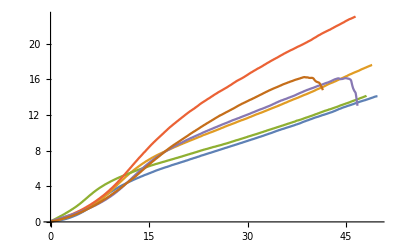

```mathematica
ListLinePlot[{sL1,sL2,sL3,sT1,sT2,sT3}]
```

### Interpolation - Stress-strain

#### 3. Average using Interpolation - sL#

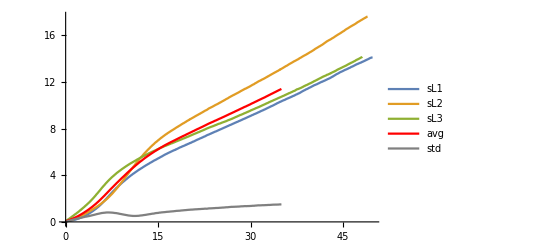

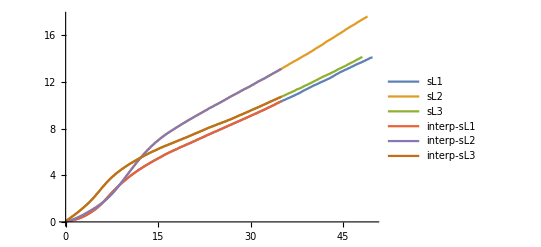

```mathematica
(*Interpolate each dataset*)
interp1=Interpolation[sL1];
interp2=Interpolation[sL2];
interp3=Interpolation[sL3];

(*Calculate the avg and std*)
avgValues=Table[Mean[{interp1[commonX[[i]]],interp2[commonX[[i]]],interp3[commonX[[i]]]}],{i,1,Length[commonX]}];
stdValues=Table[StandardDeviation[{interp1[commonX[[i]]],interp2[commonX[[i]]],interp3[commonX[[i]]]}],{i,1,Length[commonX]}];
indValues=Table[{interp1[commonX[[i]]],interp2[commonX[[i]]],interp3[commonX[[i]]]},{i,1,Length[commonX]}];

(*Combine commonX, Avg*)
avg=Table[{commonX[[i]],avgValues[[i]]},{i,1,Length[commonX]}];
std=Table[{commonX[[i]],stdValues[[i]]},{i,1,Length[commonX]}];

intpsL1=Table[{commonX[[i]],indValues[[i]][[1]]},{i,1,Length[commonX]}];
intpsL2=Table[{commonX[[i]],indValues[[i]][[2]]},{i,1,Length[commonX]}];
intpsL3=Table[{commonX[[i]],indValues[[i]][[3]]},{i,1,Length[commonX]}];

intpsLall=Table[{commonX[[i]],indValues[[i]][[1]],indValues[[i]][[2]],indValues[[i]][[3]]},{i,1,Length[commonX]}];
sL=Table[{commonX[[i]],avgValues[[i]],stdValues[[i]]},{i,1,Length[commonX]}];

ListLinePlot[{sL1,sL2,sL3,avg,std},PlotLegends->{"sL1","sL2","sL3","avg","std"},PlotStyle->{Automatic,Automatic,Automatic,Red,Gray}]
ListLinePlot[{sL1,sL2,sL3,intpsL1,intpsL2,intpsL3},PlotLegends->{"sL1","sL2","sL3","interp-sL1","interp-sL2","interp-sL3"},PlotStyle->{Automatic,Automatic,Automatic,Automatic,Automatic,Automatic}]
```

#### 3. Average using Interpolation - sT#

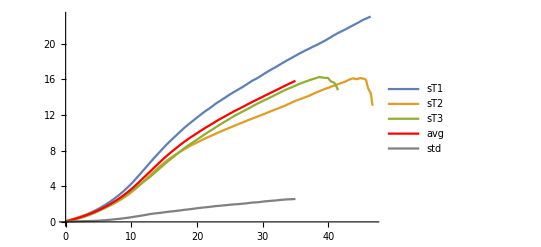

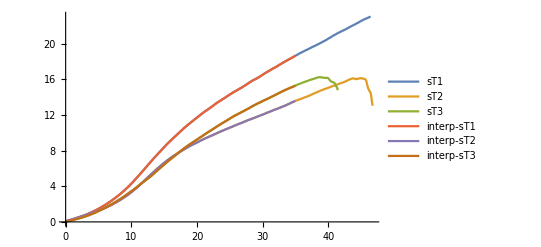

```mathematica
(*Interpolate each dataset*)
interp1=Interpolation[sT1];
interp2=Interpolation[sT2];
interp3=Interpolation[sT3];

(*Calculate the avg and std*)
avgValues=Table[Mean[{interp1[commonX[[i]]],interp2[commonX[[i]]],interp3[commonX[[i]]]}],{i,1,Length[commonX]}];
stdValues=Table[StandardDeviation[{interp1[commonX[[i]]],interp2[commonX[[i]]],interp3[commonX[[i]]]}],{i,1,Length[commonX]}];
indValues=Table[{interp1[commonX[[i]]],interp2[commonX[[i]]],interp3[commonX[[i]]]},{i,1,Length[commonX]}];

(*Combine commonX, Avg*)
avg=Table[{commonX[[i]],avgValues[[i]]},{i,1,Length[commonX]}];
std=Table[{commonX[[i]],stdValues[[i]]},{i,1,Length[commonX]}];

intpsT1=Table[{commonX[[i]],indValues[[i]][[1]]},{i,1,Length[commonX]}];
intpsT2=Table[{commonX[[i]],indValues[[i]][[2]]},{i,1,Length[commonX]}];
intpsT3=Table[{commonX[[i]],indValues[[i]][[3]]},{i,1,Length[commonX]}];

intpsTall=Table[{commonX[[i]],indValues[[i]][[1]],indValues[[i]][[2]],indValues[[i]][[3]]},{i,1,Length[commonX]}];
sT=Table[{commonX[[i]],avgValues[[i]],stdValues[[i]]},{i,1,Length[commonX]}];

ListLinePlot[{sT1,sT2,sT3,avg,std},PlotLegends->{"sT1","sT2","sT3","avg","std"},PlotStyle->{Automatic,Automatic,Automatic,Red,Gray}]
ListLinePlot[{sT1,sT2,sT3,intpsT1,intpsT2,intpsT3},PlotLegends->{"sT1","sT2","sT3","interp-sT1","interp-sT2","interp-sT3"},PlotStyle->{Automatic,Automatic,Automatic,Automatic,Automatic,Automatic}]
```

### Export

#### Export

```mathematica
(*Add additional row for Python script*)
PrependTo[sL,{1}];
PrependTo[intpsLall,{1}];
PrependTo[sT,{1}];
PrependTo[intpsTall,{1}];
```

```mathematica
Export[NotebookDirectory[]<>ToString["Interp-"]<>"sL_avg_sd.xlsx",sL]
Export[NotebookDirectory[]<>ToString["Interp-"]<>"sL_ind.xlsx",intpsLall]
Export[NotebookDirectory[]<>ToString["Interp-"]<>"sT_avg_sd.xlsx",sT]
Export[NotebookDirectory[]<>ToString["Interp-"]<>"sT_ind.xlsx",intpsTall]
```

/Users/jongcheollee/Downloads/Interpolation/Interp-sL_avg_sd.xlsx

/Users/jongcheollee/Downloads/Interpolation/Interp-sL_ind.xlsx

/Users/jongcheollee/Downloads/Interpolation/Interp-sT_avg_sd.xlsx

/Users/jongcheollee/Downloads/Interpolation/Interp-sT_ind.xlsx

/Users/jongcheollee/Downloads/Interpolation/Interp-mLs_avg_sd.xlsx

/Users/jongcheollee/Downloads/Interpolation/Interp-mLs_ind.xlsx

/Users/jongcheollee/Downloads/Interpolation/Interp-mTs_avg_sd.xlsx

/Users/jongcheollee/Downloads/Interpolation/Interp-mTs_ind.xlsx